## Testing the effectiveness of ZPS in mitigating errors for one - loss cat code

M . Bergmann and P . van Loock, PRA 94, 042332 (2016)

```mathematica
𝒜:=1/(2 Cosh[T α^2]);

p0 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]+Cos[(1-γ)T α^2]) ;
p1 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]+Sin[(1-γ)T α^2]) ;
p2 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]-Cos[(1-γ)T α^2]) ;
p3 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]-Sin[(1-γ)T α^2]) ;

𝒩:=1/(1+2Re[a b*] Cos[T α^2]/Cosh[T α^2]);

p0Tilde[a_,b_,α_,T_,γ_] = 𝒩  p0 (1+2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p1Tilde[a_,b_,α_,T_,γ_] = 𝒩  p1 (1-2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
p2Tilde[a_,b_,α_,T_,γ_] = 𝒩  p2 (1-2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p3Tilde[a_,b_,α_,T_,γ_] = 𝒩  p3 (1+2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
```

```mathematica
(* probability of correctable - including no error and uncorrectable errors(this is just 1-PC) *)
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];
PU[a_,b_,α_,T_,γ_]=p2Tilde[a,b,α,T,γ]+p3Tilde[a,b,α,T,γ];
Manipulate[
Module[{a,ℽ,b,α,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);



titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["a",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_C"
,{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{PC[a,b,α,T1,γ],PC[a,b,α,T2,γ],PC[a,-b,α,T1,γ],PC[a,-b,α,T2,γ],PC[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PC[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick},{Black, Thick},{Dashed,Gray, Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

```mathematica
(* probability of correctable errors - including no error - this is just 1-PU*)
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];

Manipulate[
Module[{a,ℽ,b,α,T,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;


ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["a",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_C"
,{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{Min[PC[a,b,α,T1,γ],PC[a,-b,α,T1,γ]],Min[PC[a,b,α,T2,γ],PC[a,-b,α,T2,γ]],Min[PC[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PC[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.00001}]
```

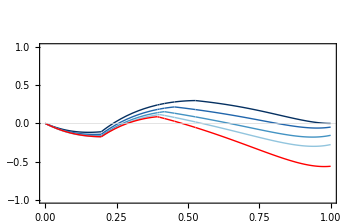

```mathematica
(* probability of correctable errors - including no error - this is just 1-PU*)
Module[{a,ℽ,func,b,α,T,T1,T2,η,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;
T2=.5;

ℽ[T_,η_]:=T/(1+(-1+T) η);

func[η_]:=Min[PC[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PC[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]-Min[PC[a,b,α,1,γ],PC[a,-b,α,1,γ]];


cols={"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};


titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["a",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.35},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["Δ(min{P_C})",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.1,1.25},{0,0}];
ylab = Graphics[{ylabel}];

plt1 = Plot[{Min[PC[a,b,α,T2,γ],PC[a,-b,α,T2,γ]]-Min[PC[a,b,α,T1,γ],PC[a,-b,α,T1,γ]],func[1-0.15],func[1-.30],func[1-.45],func[0]},{γ, 0,1},PlotRange->{-1,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,
PlotStyle->{{RGBColor[cols[[1]]],Thick},{RGBColor[cols[[2]]],Thick},{RGBColor[cols[[3]]],Thick},{RGBColor[cols[[4]]],Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None,GridLines->{None,{0}},GridLinesStyle->{Black, Thickness[.003]}];

Show[{plt1, txt,xlab,ylab}]
]
```

```mathematica
(* probability of mitigation *)
PM[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ];
Manipulate[
Module[{a,b,α,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;
ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["b",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_M",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{PM[a,b,α,T1,γ],PM[a,b,α,T2,γ],PM[a,-b,α,T1,γ],PM[a,-b,α,T2,γ],PM[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PM[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick},{Black, Thick},{Dashed,Gray, Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

```mathematica
(* probability of mitigation *)
PM[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ];
Manipulate[
Module[{a,b,α,T,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["b",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_M",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{Min[PM[a,b,α,T1,γ],PM[a,-b,α,T1,γ]],Min[PM[a,b,α,T2,γ],PM[a,-b,α,T2,γ]],Min[PM[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PM[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

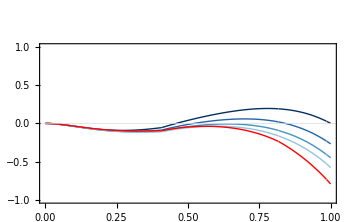

```mathematica
(* probability of mitigation *)
PM[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ];

Module[{a,b,func,α,T1,T2,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;
T2=.5;

ℽ[T_,η_]:=T/(1+(-1+T) η);

func[η_]:=Min[PM[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],PM[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]-Min[PM[a,b,α,T1,γ],PM[a,-b,α,T1,γ]];

cols={"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["b",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.35},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["Δ(min{P_M})",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.1,1.25},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{Min[PM[a,b,α,T2,γ],PM[a,-b,α,T2,γ]]-Min[PM[a,b,α,T1,γ],PM[a,-b,α,T1,γ]],func[1-0.15],func[1-0.30],func[1-0.45],func[0]},{γ, 0,1},PlotRange->{-1,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,
PlotStyle->{{RGBColor[cols[[1]]],Thick},{RGBColor[cols[[2]]],Thick},{RGBColor[cols[[3]]],Thick},{RGBColor[cols[[4]]],Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None,GridLines->{None,{0}},GridLinesStyle->{Black, Thickness[.003]}];

Show[{plt, txt,xlab,ylab}]
]
```

```mathematica
(* difference in probabilities of truly correctable errors v. uncorrectable errors *)
diff[a_,b_,α_,T_,γ_]=p1Tilde[a,b,α,T,γ]-PU[a,b,α,T,γ] ;
Manipulate[
Module[{a,b,α,ℽ,T1,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["c",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,0.52},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["(p̃)_1-P_U",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.05,0.48},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{diff[a,b,α,T1,γ],diff[a,b,α,T2,γ],diff[a,-b,α,T1,γ],diff[a,-b,α,T2,γ],diff[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],diff[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]},{γ, 0,1},PlotRange->Full,LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick},{Black, Thick},{Dashed,Gray, Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

```mathematica
(* difference in probabilities of truly correctable errors v. uncorrectable errors *)
diff[a_,b_,α_,T_,γ_]=p1Tilde[a,b,α,T,γ]-PU[a,b,α,T,γ] ;
Manipulate[
Module[{a,b,ℽ,α,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["c",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,0.52},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["(p̃)_1-P_U",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.05,0.48},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{Min[diff[a,b,α,T1,γ],diff[a,-b,α,T1,γ]],Min[diff[a,b,α,T2,γ],diff[a,-b,α,T2,γ]],Min[diff[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],diff[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]},{γ, 0,1},PlotRange->{-1,Automatic},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

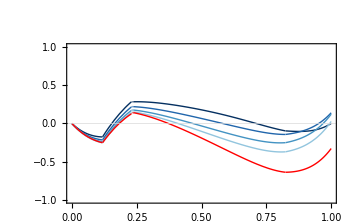

```mathematica
(* difference in probabilities of truly correctable errors v. uncorrectable errors *)
diff[a_,b_,α_,T_,γ_]=p1Tilde[a,b,α,T,γ]-PU[a,b,α,T,γ] ;

Module[{a,b,ℽ,func,α,η,T,T1,T2,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;

α = 2;

T1=1;
T2=.5;

ℽ[T_,η_]:=T/(1+(-1+T) η);

func[η_]:=Min[diff[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],diff[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]]-Min[diff[a,b,α,T1,γ],diff[a,-b,α,T1,γ]];

cols={"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["c",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.35},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["Δ(min{(p̃)_1-P_U})",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.1,1.30},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{Min[diff[a,b,α,T2,γ],diff[a,-b,α,T2,γ]]-Min[diff[a,b,α,T1,γ],diff[a,-b,α,T1,γ]],func[1-0.15],func[1-0.30],func[1-0.45],func[0]},{γ, 0,1},PlotRange->{-1,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,
PlotStyle->{{RGBColor[cols[[1]]],Thick},{RGBColor[cols[[2]]],Thick},{RGBColor[cols[[3]]],Thick},{RGBColor[cols[[4]]],Thick},{Red,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None,GridLines->{None,{0}},GridLinesStyle->{Black, Thickness[.003]}];

Show[{plt, txt,xlab,ylab}]
]
```

```mathematica
Manipulate[
Module[{a,ℽ,b,α,T1,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
a=1/(√2);
b =a;
sign =1;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";


xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["p̃",{FontSize->axesLabelSize,FontFamily->fam,Black}],{0,1.12},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{p0Tilde[a,sign b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],p1Tilde[a,sign b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],p2Tilde[a,sign b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ],p3Tilde[a,sign b,α/(√ℽ[T2,η]),T2,ℽ[T2,η]γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},PlotStyle->{{Red,Thick},{Green, Thick},{Blue,Thick},{Orange,Thick}},ImageSize->Medium,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, xlab,ylab}]
]
,{η,0,1},{T2,1,0.0001}]
```

## Noisy ZPS vs noise after ideal ZPS

Input is an even two-component cat, of the form μ̄= 𝒩_+(ⅈ^μ α+-ⅈ^μα)

```mathematica
(* noisy ZPS *)

pLnoisyZPS[α_,T_,η_]=(Cosh[T α^2]Cosh[(1-η)(1-T)α^2])/Cosh[(1-η(1-T))α^2] ; (* probaility to stay logical *)
pEnoisyZPS[α_,T_,η_]=1-pLnoisyZPS[α,T,η] ;(* probaility of an error *)

(* ZPS then loss *)

pLZPSloss[β_,T_,γ_]= pLnoisyZPS[√T β,γ,0] ; (* probability to stay logical *)
pEZPSloss[β_,T_,γ_]=1-pLZPSloss[β,T,γ] ;(* probability of an error *)
```

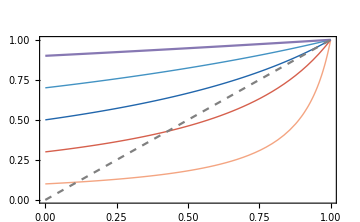

```mathematica
ClearAll[η];
Module[{γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

xlabel =Text[Style[η,{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style[η',{FontSize->axesLabelSize,FontFamily->fam,Black}],{0,1.15},{0,0}];
ylab = Graphics[{ylabel}];
plt = Plot[{ℽ[0.1,η],ℽ[0.3,η],ℽ[.5,η],ℽ[.7,η],ℽ[.9, η]},{η,0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{RGBColor["#f4a582"],Thick},{RGBColor["#d6604d"],Thick},{RGBColor["#2166ac"],Thick},{RGBColor["#4393c3"], Thick},{RGBColor["#92c5de"] Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];
Show[{plt, xlab,ylab,Plot[y,{y,0,1},PlotStyle->{Dashed, Gray}]}]
]
```

## Composition of lossy bosonic channels

Here we study the composition of two LBCs (γ1 and γ2) on an cats

From iPad notes - “Cat via noisy Threshold ZPS” we have

```mathematica
(* probability Subscript[P, xy] of x-parity cat output and y-parity cat input *)
Pee[α_,γ_]=(Cosh[(γ)α^2]Cosh[(1-γ)α^2])/Cosh[α^2];
Poe[α_,γ_]=(Sinh[(γ)α^2]Sinh[(1-γ)α^2])/Cosh[α^2];
Peo[α_,γ_]=(Cosh[(γ)α^2]Sinh[(1-γ)α^2])/Sinh[α^2];
Poo[α_,γ_]=(Sinh[(γ)α^2]Cosh[(1-γ)α^2])/Sinh[α^2];
```

```mathematica
p1 =Simplify[Pee[√γ1 α,γ2]Pee[α,γ1]+Peo[√γ1 α,γ2]Poe[α,γ1]]
p2 =Simplify[Poe[√γ1 α,γ2]Pee[α,γ1]+Poo[√γ1 α,γ2]Poe[α,γ1]]
```

Cosh[α^2 γ1 γ2] Cosh[α^2 (1-γ1 γ2)] Sech[α^2]

Sech[α^2] Sinh[α^2 γ1 γ2] Sinh[α^2 (1-γ1 γ2)]

This tells that the effective transmission is simply the product of the two transmissions